```mathematica
fa[x_,a_]:=(2 a/Pi)^(3/4)E^(-a Abs[x-0]^2);fb[x_,b_]:=(2 b/Pi)^(3/4)E^(-b Abs[x-.5]^2);
fc:=fa[x,a]*fb[x,b]
```

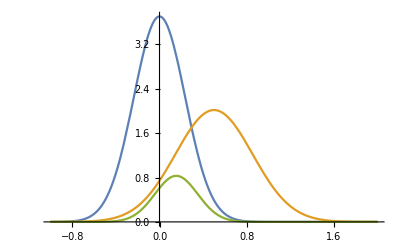

```mathematica
Plot[{fa[x,9],fb[x,4],fa[x,9]*fb[x,4]/4.5},{x,-1,2},PlotRange->Full]
```

```mathematica
fa[-.2,9]
```

2.58372

```mathematica
fb[.7,4]
```

1.71778

```mathematica
fa[.15,9]*fb[.15,4]/4.5
```

0.830014

```mathematica
FindMaximum[fa[x,9]*fb[x,4],x]
```

{3.73578,{x→0.153846}}